# AlgebraicRange

Generate ranges of algebraic numbers

## Definition

### Helper functions

#### FormulaComplexity

```mathematica
ClearAll[formulaComplexity,formulaComplexityHeuristic]

(*this option can be used for internal testing*)
(*Options[formulaComplexity]={Method->"Heuristic"};*)
(*the BuiltIn Method with SimplifyCount has the fundamental problem of not being continuous and thus of not allowing fine tuning*)

digitSum[int_Integer]:=If[$VersionNumber>=14,DigitSum[int],Total@IntegerDigits[int]]

formulaComplexityHeuristic[form_?NumericQ]:=
	N@Total[Cases[
			Inactivate[form]
		/.const_?(Quiet@MemberQ[Attributes[#],Constant]&):>1
			/.c_Complex:>ReIm[c]
				/.r:Rational[i1_Integer,i2_Integer]:>{i1,i2}
					/.Inactive[Sqrt][arg_]:>Inactive[Sqrt[{arg,arg}]]
						/.Alternatives[
							Inactive[Power][b_,Inactive[Times][m_,Inactive[Power][n_,-1]]|{m_,n_}],
							Inactive[Power][{b_},Inactive[Times][m_,Inactive[Power][n_,-1]]|{m_,n_}]]:>
								Table[b,Abs[n]+Abs[m]],
			_Integer,{0,Infinity}]/. j_Integer?NonPositive:>-j+1
				/.i_Integer:>Mean[1/2{5IntegerLength[i],digitSum[i],Total[Last/@FactorInteger[i]],Sqrt[Abs[N[i]]]}]]

(*from ComplexityFunction documentation*)
(*SimplifyCount[p_]:=
Which[Head[p]===Symbol,1,
IntegerQ[p],If[p==0,1,Floor[N[Log[2,Abs[p]]/Log[2,10]]]+If[p>0,1,2]],
Head[p]===Rational,SimplifyCount[Numerator[p]]+SimplifyCount[Denominator[p]]+1,
Head[p]===Complex,SimplifyCount[Re[p]]+SimplifyCount[Im[p]]+1,NumberQ[p],2,
True,SimplifyCount[Head[p]]+If[Length[p]==0,0,Plus@@(SimplifyCount/@(List@@p))]]*)

(*formulaComplexity[form_?NumericQ,opts:OptionsPattern[formulaComplexity]]:=
	Switch[OptionValue[Method],
		"BuiltIn",
			SimplifyCount[form],
		"Heuristic",
			formulaComplexityHeuristic[form]]*)

formulaComplexity[form_?NumericQ]:=
	formulaComplexityHeuristic[form]
```

#### Utilities

```mathematica
realReplace[x_]:=If[Head[x]===Real,RootApproximant[x],x]
```

#### Error management

```mathematica
failureNotReal=
Failure["NotReal",<|"MessageTemplate"->"The input parameters `nr` are not real numbers.","MessageParameters"-><|"nr"->#|>|>]&;
failureNotAlg=Failure["NotAlgebraic",<|"MessageTemplate"->"The input parameters `na` are not algebraic numbers.","MessageParameters"-><|"na"->#|>|>]&;
failureFareyStep=Failure["FareyStep",<|"MessageTemplate"->"The step parameter `s` is not allowed with the Farey range option.","MessageParameters"-><|"s"->#|>|>]&;
failureLowerBound=
	Failure["LowerBound",<|"MessageTemplate"->"The steps' lower bound parameter `d` cannot be negative.","MessageParameters"-><|"d"->#|>|>]&;
failureUpperBound=
Failure["UpperLowerBound",<|"MessageTemplate"->"The steps' upper bound `s` cannot be lower than the lower bound `d` in absolute value.","MessageParameters"-><|"s"->#1,"d"->#2|>|>]&;
```

```mathematica
failureThrow[arg_]:=
	If[MemberQ[arg,_Failure|$Failed,{0,Infinity}],
		Throw@First@Union@Cases[arg,_Failure|$Failed,{0,Infinity}],
		arg]
```

### Basic range

#### Farey range

```mathematica
ClearAll[fareyRange]
fareyRange[r1_,r2_,r3_]:=
	If[r3>=1,
		ResourceFunction["FareyRange"][r1,r2,r3],
		Which[(*intuitive alternative step*)
			MatchQ[r3,Rational[1,_]],
				ResourceFunction["FareyRange"][r1,r2,1/r3],
			MatchQ[r3,Rational[-1,_]],
				Reverse[ResourceFunction["FareyRange"][r2,r1,-1/r3]],
			True,
				failureFareyStep[r3]]]
```

#### Elementary range

```mathematica
ClearAll[elemRange]

elemRange[{ord_},{r1_},opts:OptionsPattern[AlgebraicRange]]/;r1>=1:=
	Range[1,r1^ord]^(1/ord)
elemRange[{ord_},{r1_},opts:OptionsPattern[AlgebraicRange]]/;r1<1:=
	{}

elemRange[{ord_},{r1_,r2_},opts:OptionsPattern[AlgebraicRange]]/;0<=r1<=r2:=
	Range[r1^ord,r2^ord]^(1/ord)
elemRange[{ord_},{r1_,r2_},opts:OptionsPattern[AlgebraicRange]]/;r1<0&&r2>=0:=
	Join[-elemRange[{ord},{0,-r1},opts],elemRange[{ord},{0,r2},opts]]//cleanSort
elemRange[{ord_},{r1_,r2_},opts:OptionsPattern[AlgebraicRange]]/;r1<=r2<=0:=
	-elemRange[{ord},{-r2,-r1},opts]//cleanSort
elemRange[{ord_},{r1_,r2_},opts:OptionsPattern[AlgebraicRange]]/;r2<r1:=
	{}

elemRange[{ord_},{r1_,r2_,-1},opts:OptionsPattern[AlgebraicRange]]/;r1>=r2>=0:=
	Range[r1^ord,r2^ord,-1]^(1/ord)
elemRange[{ord_},{r1_,r2_,-1},opts:OptionsPattern[AlgebraicRange]]/;r2<0&&r1>=0:=
	Join[-elemRange[{ord},{-r2,0,-1},opts],elemRange[{ord},{r1,0,-1},opts]]//cleanSort//Reverse
elemRange[{ord_},{r1_,r2_,-1},opts:OptionsPattern[AlgebraicRange]]/;r2<=r1<=0:=
	-elemRange[{ord},{-r2,-r1,-1},opts]//cleanSort//Reverse
elemRange[{ord_},{r1_,r2_,-1},opts:OptionsPattern[AlgebraicRange]]/;r2>r1:=
	{}

(*the remaining definitions below are used only for the option "StepMethod"->"Root"*)


elemRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;0<=r1<=r2&&r3>0:=
	If[!OptionValue["FareyRange"],
		Range[r1^ord,r2^ord,r3^ord]^(1/ord),
		fareyRange[r1^ord,r2^ord,r3^ord]^(1/ord)]


elemRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;r1<0&&r2>=0&&r3>0&&r3<=r2-r1:=
	Join[-elemRange[{ord},{0,-r1,r3},opts],elemRange[{ord},{0,r2,r3},opts]]//cleanSort

elemRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;r1<0&&r2>=0&&r3>0&&r3>r2-r1:=
	{r1}

elemRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;r1<=r2<=0&&r3>0:=
	-elemRange[{ord},{-r2,-r1,r3},opts]


elemRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;0<=r2<=r1&&r3<0:=
	Range[r1^ord,r2^ord,-(-r3)^ord]^(1/ord)

elemRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;r2<0&&r1>=0&&r3<0&&Abs[r3]<=r1-r2:=
	Join[-elemRange[{ord},{-r2,0,r3},opts],elemRange[{ord},{r1,0,r3},opts]]//cleanSort//Reverse
elemRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;r2<0&&r1>=0&&r3<0&&Abs[r3]>r1-r2:=
	{r1}



elemRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;r2<=r1<=0&&r3<0:=
	-elemRange[{ord},{-r1,-r2,-r3},opts]

elemRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;r2<r1&&r3>=0:=
	{}
elemRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;r1<r2&&r3<=0:=
	{}
```

#### Step range

```mathematica
ClearAll[factorRange]
factorRange[{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]:=
	Block[{max,as,one},
	max=Max[Abs[r1],Abs[r2]];
	as=Abs[r3];
	one=Max[1,as];
	If[!OptionValue["FareyRange"],
		Join[DeleteCases[Range[one,0,-as],1],Range[one,max,as]],
		Join[DeleteCases[fareyRange[one,0,-as],1],fareyRange[one,max,as]]//failureThrow]]
```

```mathematica
ClearAll[outerRange]
outerRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;r1<=r2&&r3>0&&r3<=Max[Abs[r1],Abs[r2]]:=
	Select[
	Outer[
		Times,
		elemRange[{ord},{If[r3<=1,r1,r1/r3],r2},opts],
		factorRange[{r1,r2,r3},opts]
		]//Flatten//cleanSort,
	r1<=#<=r2&]
outerRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;r2<=r1&&r3<0&&Abs[r3]<=Max[Abs[r1],Abs[r2]]:=
	Select[
	Outer[
		Times,
		elemRange[{ord},{If[r3>=-1,r1,-r1/r3],r2,-1},opts],
		factorRange[{r1,r2,r3},opts]
		]//Flatten//cleanSort//Reverse,
	r2<=#<=r1&]
outerRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;r2<r1&&r3>=0:=
	{}
outerRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;r1<=r2&&r3<=0:=
	{}
outerRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;r1<=r2&&r3>0&&r3>Max[Abs[r1],Abs[r2]]:=
	{r1}
outerRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;r2<=r1&&r3<0&&Abs[r3]>Max[Abs[r1],Abs[r2]]:=
	{r1}
```

```mathematica
ClearAll[stepRange]
stepRange[{ord_},{r1_,r2_,r3_:1},opts:OptionsPattern[AlgebraicRange]]:=
	Which[
	OptionValue["StepMethod"]==="Outer",
		outerRange[{ord},{r1,r2,r3},opts],	
	OptionValue["StepMethod"]==="Root",
		elemRange[{ord},{r1,r2,r3},opts]]
```

#### Restricted range

```mathematica
cleanSort[list_List]:=SortBy[DeleteDuplicatesBy[list,N],N]
```

```mathematica
ClearAll[stepSelect,complexitySelect]

complexitySelect[list_List,c_]:=
	Select[list,formulaComplexity[#]<=c&]

stepSelect[list_List,d_]:=
	Block[{sel,eln,i},
	eln=list[[1]];
	sel={eln};
	
	For[i=2,i<=Length[list],i++,
		
		If[Abs[list[[i]]-eln]>=d,

			eln=list[[i]];
			AppendTo[sel,eln],
			
			Continue[]]];
	
	sel]~Quiet~N::meprec

stepSelect[{},d_,t_:0]:=
	{}
```

```mathematica
restrictRange[main_,compl_,d_:0]:=
	DeleteDuplicatesBy[If[d!=0,stepSelect[#,d],#]&[complexitySelect[main,compl]],N]
```

### Main definition

```mathematica
ClearAll[AlgebraicRange,iAlgebraicRange]

Options[AlgebraicRange]={"RootOrder"->2,"FareyRange"->False,"FormulaComplexity"->Infinity,"StepMethod"->"Outer","AlgebraicsOnly"->True};

(*internal main function*)

iAlgebraicRange[{ord_?NumericQ},{r1_,r2_,r3_:1},d_:0,opts:OptionsPattern[AlgebraicRange]]/;ord>=1:=
	Block[{o,x,y,s,mainrange,fullrange},

		{o,x,y,s}=realReplace/@{ord,r1,r2,r3};

		If[!Element[{o,x,y,s},Reals],
			Failure["NotReal",
						failureNotReal[Select[{o,x,y,s},!Element[#,Reals]&]]]//failureThrow];

		If[!Element[{o,x,y,s},Algebraics]&&OptionValue["AlgebraicsOnly"],
			Failure["NotAlgebraic",
						failureNotAlg[Select[{o,x,y,s},!Element[#,Algebraics]&]]]//failureThrow];

		If[d>Abs[r3],
			failureUpperBound[r3,d]//failureThrow];
		
		mainrange=If[r3===1,
					elemRange[{o},{x,y}],
					stepRange[{o},{x,y,s},opts]];

		fullrange=mainrange
		(*in the extended paclet version here combinations of the basic range are made*);

		restrictRange[fullrange,OptionValue["FormulaComplexity"],d]//failureThrow]//Catch

iAlgebraicRange[ordL_List,rL_List,d_:0,opts:OptionsPattern[AlgebraicRange]]/;(Length[ordL]>=2&&d>=0):=
	Block[{stepNegQ,join,sort},
	stepNegQ=Length[rL]==3&&rL[[3]]<0;
	join=Join@@Map[failureThrow@iAlgebraicRange[{#},rL,d,opts]&,ordL];
	sort=If[stepNegQ,Reverse[#],#]&@cleanSort@join;
	If[d!=0,stepSelect[sort,d],sort]]//Catch

iAlgebraicRange[ord_Integer,rL_List,d_:0,opts:OptionsPattern[AlgebraicRange]]/;d>=0:=
	iAlgebraicRange[Range[2,ord],rL,d,opts]


(*external main function*)

AlgebraicRange[r1_?NumericQ,r2_?NumericQ,r3_:1,d_:0,opts:OptionsPattern[AlgebraicRange]]/;NumericQ[r3]&&d>=0:=
	iAlgebraicRange[OptionValue["RootOrder"],{r1,r2,r3},d,opts]

AlgebraicRange[r1_?NumericQ,opts:OptionsPattern[AlgebraicRange]]:=
	iAlgebraicRange[OptionValue["RootOrder"],{1,r1,1},0,opts]

AlgebraicRange[_,_,_,d_,opts:OptionsPattern[AlgebraicRange]]/;d<0:=
	failureLowerBound[d]
```

## Documentation

### Usage

AlgebraicRange[x]

gives the range of square roots Sqrt[Range[1,x^2]], for x>=1.

AlgebraicRange[x,y]

gives the range of square roots Sqrt[Range[x^2,y^2]], for 0<=x<=y.

AlgebraicRange[x,y,s]

generates steps bounded above by s, with 0<s<=y.

AlgebraicRange[x,y,s,d]

requires the steps to be bounded below by d, with 0<=d<=s.

### Details & Options

AlgebraicRange creates ranges made of algebraic numbers. This extends the basic concept of Range to include, besides Rational numbers, also roots, always restricted to the Reals domain.

The first two arguments represent the bounds of the range (minimum and maximum values), while the optional third and fourth arguments (by default equal to 1 and 0) regulate the upper and lower bounds of the steps (differences between successive elements).

If no step parameter is specified, the elementary algebraic range AlgebraicRange[x,y] is determined by the square root range Sqrt[Range[x^2,y^2]], for x,y>0. The extension to negative bounds x <0 or y<0 is performed simply by reflection, since general real roots are mathematically defined only for positive arguments.

The step between successive algebraics is not straightforward to define univocally, as there exists no constant difference among the irrational numbers generated even with the elementary algebraic range. However, it turns out that an intuitively simple class of algebraic ranges, with non-unit step parameter s, is obtained by taking the outer product of AlgebraicRange[Min[x,x/s],y] with Join[ Range[Max[1, s], y, s],Range[Max[1, s], 0, -s]], for s>0 and 0<=x<=y. Then the parameter s also becomes the upper bound for all the steps. For example, AlgebraicRange[0,2,1/2]={0,1/2,1/(√2),(√3)/2,1,√2,3/2,√3,2}.

The algebraic numbers thus generated can often be in a great number, with a tendency to accumulate towards certain points. To avoid these features, a further fourth argument d can be optionally provided to require a minimum (absolute value) difference between successive algebraics, that is a lower bound for all the steps. This truncation process typically leads to a nearly uniform distribution of numeric values.

Extended functionality and syntax, especially for creating algebraic numbers of a more general form, are provided in the homonymous function of the paclet DanieleGregori/GeneralizedRange.

A natural application of AlgebraicRange is in the search for closed forms for floating point numbers, possibly in terms of arbitrary combinations of mathematical functions with algebraic arguments, through ResourceFunction["FindClosedForm"].

AlgebraicRange accepts the following options:

"RootOrder" | 2 | the root orders to be included
"StepMethod" | "Outer" | change the method to define the step
"FareyRange" | False | generate algebraic numbers with steps given by the Farey sequence
"FormulaComplexity" | Infinity | set a complexity threshold over which the algebraics are discarded
"AlgebraicsOnly" | True | accept only algebraic arguments and output

The option "RootOrder" can take the following values:

r | include roots up to r order
{r} | include only roots of order r
{r_1,r_2,…} | include roots of all specified orders r_k

The option "StepMethod" can be used to define the step in AlgebraicRange[x,y,s] and can take the following values:

"Outer" | take the Outer product of AlgebraicRange[Min[x,x/s],y] with Join[ Range[Max[1, s], y, s],Range[Max[1, s], 0, -s]]
"Root" | use Sqrt[Range[x^2,y^2,s^2]]

A more detailed explanation of the step definition, also for negative bounds, can be found in the Properties and Relations Examples subsection.

Besides using the fourth argument to impose a lower bound on the steps, another way to restrict the output of AlgebraicRange is by setting a threshold for the complexity of the numeric expressions involved through the option "FormulaComplexity". The heuristic prescription for computing such complexity values is the following:
i) take all Integers appearing in the algebraic expression; 
ii) if a root or Power appears, duplicate its argument a number of times equal to the root or power degree;
iii) if a negative integer or 0 appears, take its opposite and add 1;
iv) for each positive integer, compute the Mean among its DigitSum, 5 times its IntegerLength, the total number of its prime factors and the square root of its absolute value;
v) normalize these means by multiplying them by 1/2 (so to let the numbers 0 and 1 have unit complexity);
vi) take the Total of all these means.

## Examples

### Basic Examples

Generate a range of square roots:

```mathematica
range=AlgebraicRange[3]
```

{1,√2,√3,2,√5,√6,√7,2 √2,3}

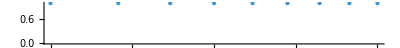

```mathematica
NumberLinePlot[range]
```

Generate a square root range with non-unit step:

```mathematica
range=AlgebraicRange[0,3,1/2]
```

{0,1/2,1/(√2),(√3)/2,1,(√5)/2,√(3/2),(√7)/2,√2,3/2,√3,2,3/(√2),√5,√6,5/2,(3 √3)/2,√7,2 √2,3}

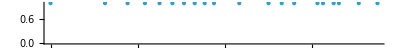

```mathematica
NumberLinePlot[range]
```

### Scope

Generate a range of negative square roots:

```mathematica
range=AlgebraicRange[-3,-1]
```

{-3,-2 √2,-√7,-√6,-√5,-2,-√3,-√2,-1}

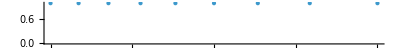

```mathematica
NumberLinePlot[range]
```

Generate a range of mixed positive and negative roots, with a negative step:

```mathematica
range=AlgebraicRange[2,-2,-1/2]
```

{2,√3,3/2,√2,1,(√3)/2,1/(√2),1/2,0,-1/2,-1/(√2),-(√3)/2,-1,-√2,-3/2,-√3,-2}

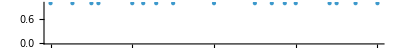

```mathematica
NumberLinePlot[range]
```

Generate a range of square roots, with certain upper and lower bounds on the steps:

```mathematica
range=AlgebraicRange[2,7,1/3,1/4]
```

{2,(√46)/3,2 √(5/3),(2 √19)/3,√10,2 √3,(5 √5)/3,4,(2 √41)/3,(2 √46)/3,√23,√26,√29,4 √2,√35,(7 √7)/3,5 √(5/3),3 √5,7}

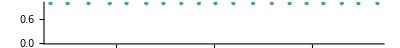

```mathematica
NumberLinePlot[range]
```

```mathematica
N@MinMax@Differences[range]
```

{0.252804,0.323944}

Generate a range of nested square roots:

```mathematica
AlgebraicRange[Sqrt[1+Sqrt[2]],4,1/Sqrt[2]]
```

{√(1+√2),√(2+√2),√(3+√2),√(4+√2),√(5+√2),(1+1/(√2)) √(1+√2),√(6+√2),√(7+√2),√(8+√2),(1+1/(√2)) √(2+√2),√(9+√2),√(10+√2),√(11+√2),(1+1/(√2)) √(3+√2),√(12+√2),(1+√2)^(3/2),√(13+√2),√(14+√2),(1+1/(√2)) √(4+√2)}

### Options

#### RootOrder

Generate a range of square and cubic roots:

```mathematica
AlgebraicRange[2,"RootOrder"->3]
```

{1,2^(1/3),√2,3^(1/3),2^(2/3),5^(1/3),√3,6^(1/3),7^(1/3),2}

Generate a range of fourth roots:

```mathematica
AlgebraicRange[0,4,2,"RootOrder"->{4}]
```

{0,2,2 2^(1/4),2 3^(1/4),2 √2,2 5^(1/4),2 6^(1/4),2 7^(1/4),2 2^(3/4),2 √3,2 10^(1/4),2 11^(1/4),2 √2 3^(1/4),2 13^(1/4),2 14^(1/4),2 15^(1/4),4}

Generate a range of cube and fifth roots:

```mathematica
AlgebraicRange[1,3/2,"RootOrder"->{3,5}]
```

{1,2^(1/5),3^(1/5),2^(1/3),2^(2/5),5^(1/5),6^(1/5),3^(1/3),7^(1/5)}

Generate algebraic terms up to fourth root order and require a minimum absolute difference between successive roots:

```mathematica
AlgebraicRange[0,4,2,1/4,"RootOrder"->4]
```

{0,2,2 2^(1/4),2 3^(1/4),2 3^(1/3),2 2^(2/3),2 √3,2 14^(1/4)}

#### StepMethod

Change method to define the step:

```mathematica
root=AlgebraicRange[0,3,1/3,"StepMethod"->"Root"]
```

{0,1/3,(√2)/3,1/(√3),2/3,(√5)/3,√(2/3),(√7)/3,(2 √2)/3,1,(√10)/3,(√11)/3,2/(√3),(√13)/3,(√14)/3,√(5/3),4/3,(√17)/3,√2,(√19)/3,(2 √5)/3,√(7/3),(√22)/3,(√23)/3,2 √(2/3),5/3,(√26)/3,√3,(2 √7)/3,(√29)/3,√(10/3),(√31)/3,(4 √2)/3,√(11/3),(√34)/3,(√35)/3,2,(√37)/3,(√38)/3,√(13/3),(2 √10)/3,(√41)/3,√(14/3),(√43)/3,(2 √11)/3,√5,(√46)/3,(√47)/3,4/(√3),7/3,(5 √2)/3,√(17/3),(2 √13)/3,(√53)/3,√6,(√55)/3,(2 √14)/3,√(19/3),(√58)/3,(√59)/3,2 √(5/3),(√61)/3,(√62)/3,√7,8/3,(√65)/3,√(22/3),(√67)/3,(2 √17)/3,√(23/3),(√70)/3,(√71)/3,2 √2,(√73)/3,(√74)/3,5/(√3),(2 √19)/3,(√77)/3,√(26/3),(√79)/3,(4 √5)/3,3}

Compare with the default "Outer" step method:

```mathematica
outer=AlgebraicRange[0,3,1/3]
```

{0,1/3,(√2)/3,1/(√3),2/3,(√5)/3,√(2/3),(√7)/3,(2 √2)/3,1,2/(√3),4/3,√2,(2 √5)/3,2 √(2/3),5/3,√3,(2 √7)/3,(4 √2)/3,2,√5,4/(√3),7/3,(5 √2)/3,√6,√7,8/3,2 √2,5/(√3),(4 √5)/3,3}

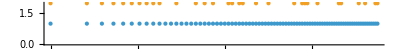

```mathematica
NumberLinePlot[{root, outer},PlotLegends->{"Root","Outer"}]
```

In general, the default range is a subset of this other:

```mathematica
SubsetQ[root,outer]
```

True

#### FareyRange

Generate an algebraic range that generalizes ResourceFunction["FareyRange"]:

```mathematica
algrange=AlgebraicRange[0,3,1/3,"FareyRange"->True]
```

{0,1/3,(√2)/3,1/2,1/(√3),2/3,1/(√2),(√5)/3,√(2/3),(√3)/2,(√7)/3,(2 √2)/3,1,(√5)/2,2/(√3),√(3/2),(√7)/2,4/3,√2,(2 √5)/3,3/2,2 √(2/3),5/3,√3,(2 √7)/3,(4 √2)/3,2,3/(√2),√5,4/(√3),7/3,(5 √2)/3,√6,5/2,(3 √3)/2,√7,8/3,2 √2,5/(√3),(4 √5)/3,3}

```mathematica
fareyrange=ResourceFunction["FareyRange"][0,3,3]
```

{0,1/3,1/2,2/3,1,4/3,3/2,5/3,2,7/3,5/2,8/3,3}

```mathematica
SubsetQ[algrange,fareyrange]
```

True

Notice that the step parameter is originally the denominator of the step (both it and its reciprocal are accepted). This corresponds to the Union of ranges with steps equal to the elements of the FareySequence:

```mathematica
FareySequence[3]//DeleteCases[#,0]&
```

{1/3,1/2,2/3,1}

```mathematica
SortBy[Union@Flatten@Map[AlgebraicRange[0,3,#]&,%],N]==AlgebraicRange[0,3,3,"FareyRange"->True]
```

True

#### FormulaComplexity

With the default option "FormulaComplexity" set to Infinity, a very large number of algebraics can be produced:

```mathematica
AlgebraicRange[1,4,1,"RootOrder"->4]//Short
```

{1,2^(1/4),2^(1/3),3^(1/4),√2,3^(1/3),5^(1/4),6^(1/4),2^(2/3),7^(1/4),2^(3/4),«294»,247^(1/4),2^(3/4) 31^(1/4),249^(1/4),2^(1/4) 5^(3/4),3^(2/3) 7^(1/3),251^(1/4),√6 7^(1/4),253^(1/4),254^(1/4),255^(1/4),4}

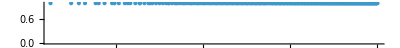

```mathematica
NumberLinePlot[%]
```

One way to limit these is by using the fourth argument, to require a minimum absolute difference between successive algebraics:

```mathematica
AlgebraicRange[1,4,1,1/10,"RootOrder"->4]
```

{1,2^(1/4),3^(1/4),3^(1/3),2^(2/3),5^(1/3),6^(1/3),15^(1/4),19^(1/4),23^(1/4),√2 7^(1/4),14^(1/3),2^(3/4) 5^(1/4),47^(1/4),55^(1/4),2 √2,74^(1/4),85^(1/4),97^(1/4),110^(1/4),5^(3/4),141^(1/4),159^(1/4),178^(1/4),199^(1/4),222^(1/4),246^(1/4)}

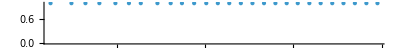

```mathematica
NumberLinePlot[%]
```

An alternative way is by setting the option "FormulaComplexity" to a finite threshold value, to select only numeric symbols with complexity less than that:

```mathematica
AlgebraicRange[4,"RootOrder"->4,"FormulaComplexity"->8]
```

{1,2^(1/4),2^(1/3),3^(1/4),√2,3^(1/3),2^(2/3),5^(1/3),√3,6^(1/3),7^(1/3),2,3^(2/3),√5,2 2^(1/4),√6,2 2^(1/3),2 3^(1/4),√7,2 √2,2 3^(1/3),3,√10,2 2^(2/3),√11,2 5^(1/3),2 √3,3 2^(1/4),√13,√14,3 2^(1/3),4}

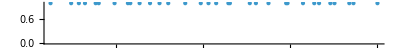

```mathematica
NumberLinePlot[%]
```

#### AlgebraicsOnly

By default, only algebraic numbers are accepted as input parameters:

```mathematica
AlgebraicRange[0,5,Sqrt[E]]
```

Failure[…]

Set this option to deliberately accept an output range which includes transcendental numbers:

```mathematica
AlgebraicRange[0,5,Sqrt[E],"AlgebraicsOnly"->False]
```

{0,√ⅇ,√(2 ⅇ),√(3 ⅇ),2 √ⅇ,√(5 ⅇ),√(6 ⅇ),√(7 ⅇ),2 √(2 ⅇ),3 √ⅇ}

```mathematica
Element[%,Algebraics]
```

False

### Applications

AlgebraicRange[x,y] is naturally suited for searching possible closed forms through ResourceFunction["FindClosedForm"]:

```mathematica
ResourceFunction["FindClosedForm"][1.05592,BarnesG,"SearchRange"->Function[AlgebraicRange[-#,#,"RootOrder"->4]]]
```

BarnesG[2^(1/4)]

```mathematica
N[%]
```

1.05592

Compare with the more complex result found with the "Plain" rational range:

```mathematica
ResourceFunction["FindClosedForm"][1.05592,BarnesG,"SearchRange"->"Plain"]
```

-1/63+BarnesG[4/3]

```mathematica
N[%]
```

1.05591

AlgebraicRange[x,y,s] provides a more general search range:

```mathematica
AlgebraicRange[-3,3,1/3,"RootOrder"->4]//Short
```

{-3,-2 5^(1/4),-(4 √5)/3,-79^(1/4),-78^(1/4),-(4 11^(1/3))/3,-(5 10^(1/4))/3,-26^(1/3),-77^(1/4),-√2 19^(1/4),«682»,77^(1/4),26^(1/3),(5 10^(1/4))/3,(4 11^(1/3))/3,78^(1/4),79^(1/4),(4 √5)/3,2 5^(1/4),3}

```mathematica
MemberQ[%,4/3]
```

True

The built-in function RootApproximant may have difficulty recognizing even relatively simple nested roots:

```mathematica
N[4 √(5+√2),10]
```

10.13051909

```mathematica
RootApproximant[%]//ToRadicals
```

1/17 (83+2 √1990)

In principle, these may be recognized by equipping ResourceFunction["FindClosedForm"] with a suitable search range in terms of AlgebraicRange[x,y,s]:

```mathematica
ResourceFunction["FindClosedForm"][10.13051909,Identity,"SearchRange"->Function[Join[AlgebraicRange[1,#,1/2],AlgebraicRange[Sqrt[1+Sqrt[2]],#,1/Sqrt[2]]]]]
```

4 √(5+√2)

### Properties and Relations

AlgebraicRange[x,y] extends Range[x,y]:

```mathematica
algrange=AlgebraicRange[2,5]
```

{2,√5,√6,√7,2 √2,3,√10,√11,2 √3,√13,√14,√15,4,√17,3 √2,√19,2 √5,√21,√22,√23,2 √6,5}

```mathematica
range=Range[2,5]
```

{2,3,4,5}

```mathematica
SubsetQ[algrange,range]
```

True

AlgebraicRange[x,y] for x<=y<0 is equivalent to Reverse[-AlgebraicRange[-y,-x]]:

```mathematica
AlgebraicRange[-3,-1]
```

{-3,-2 √2,-√7,-√6,-√5,-2,-√3,-√2,-1}

```mathematica
Reverse[-AlgebraicRange[1,3]]
```

{-3,-2 √2,-√7,-√6,-√5,-2,-√3,-√2,-1}

Compute the algebraic range for 0<=x<=y and positive step upper bound s>0:

```mathematica
AlgebraicRange[1,3,1/2]
```

{1,(√5)/2,√(3/2),(√7)/2,√2,3/2,√3,2,3/(√2),√5,√6,5/2,(3 √3)/2,√7,2 √2,3}

This is an equivalent calculation:

```mathematica
Select[SortBy[Outer[Times,Range[0,3,1/2],AlgebraicRange[1,3]]//Flatten//DeleteDuplicates,N],1<=#<=3&]
```

{1,(√5)/2,√(3/2),(√7)/2,√2,3/2,√3,2,3/(√2),√5,√6,5/2,(3 √3)/2,√7,2 √2,3}

An algebraic range with a negative irrational step size:

```mathematica
AlgebraicRange[3,3/2,-1/Sqrt[3]]
```

{3,2 √2,√3 (1+1/(√3)),√7,√6,√5,√2 (1+1/(√3)),2,√3}

An equivalent calculation:

```mathematica
Select[ReverseSortBy[Outer[Times,Join[Range[1,3,1/Sqrt[3]],Range[1,0,-1/Sqrt[3]]],Range[3^2,(3/2)^2,-1]^(1/2)]//Flatten//DeleteDuplicates,N],3/2<=#<=3&]
```

{3,2 √2,√3 (1+1/(√3)),√7,√6,√5,√2 (1+1/(√3)),2,√3}

Because of this peculiar definition, a negative step is not always equivalent to the reversed positive step:

```mathematica
AlgebraicRange[3/2,-3/2,-1/3]
```

{3/2,(2 √5)/3,(√5)/2,1,(√5)/3,2/3,1/2,(√5)/6,1/3,1/6,0,-1/6,-1/3,-(√5)/6,-1/2,-2/3,-(√5)/3,-1,-(√5)/2,-(2 √5)/3,-3/2}

```mathematica
AlgebraicRange[-3/2,3/2,1/3]//Reverse
```

{√2,4/3,1,(2 √2)/3,2/3,(√2)/3,1/3,0,-1/3,-(√2)/3,-2/3,-(2 √2)/3,-1,-4/3,-√2}

As a general rule, a positive starting point is always preserved:

```mathematica
AlgebraicRange[Sqrt[10],-Sqrt[10],-2]
```

{√10,√6,√2,0,-2,-2 √2}

```mathematica
AlgebraicRange[2Sqrt[2+Sqrt[3]],-2Sqrt[2+Sqrt[3]],-Sqrt[5]]//Simplify
```

{2 √(2+√3),√(3+4 √3),√(-2+4 √3),0,-√(-30+20 √3),-√(5 (-5+4 √3)),-2 √(5 (-1+√3))}

The numbers generated always belong to the domains of Algebraics and Reals:

```mathematica
algrange=Block[{$MaxExtraPrecision=10000},AlgebraicRange[2Sqrt[1+Sqrt@RandomInteger[{2,4}]],-2Sqrt[1+Sqrt@RandomInteger[{2,4}]],-Sqrt[2]/RandomInteger[{2,4}],1/4,"RootOrder"->RandomInteger[{2,5},2]]]
```

{2 √(1+√2),(-27+16 (1+√2)^2)^(1/4),(-48+16 (1+√2)^2)^(1/4),(-64+16 (1+√2)^2)^(1/4),(-75+16 (1+√2)^2)^(1/4),(1-1/(2 √2)) (-31+16 (1+√2)^2)^(1/4),(1-1/(2 √2)) (-59+16 (1+√2)^2)^(1/4),(1-1/(2 √2)) (-77+16 (1+√2)^2)^(1/4),(1-1/(2 √2)) (-87+16 (1+√2)^2)^(1/4),(1-1/(√2)) (-45+16 (1+√2)^2)^(1/4),(1-1/(√2)) (-84+16 (1+√2)^2)^(1/4),(1-1/(√2)) (-93+16 (1+√2)^2)^(1/4),-((1-1/(√2)) (-41+24 √3)^(1/3)),-((1-1/(√2)) (-36+24 √3)^(1/3)),-((1-1/(√2)) (-23+24 √3)^(1/3)),-7^(1/4) (1-1/(2 √2)),-17^(1/4) (1-1/(2 √2)),-6^(1/4),-11^(1/4),-106^(1/4) (1-1/(2 √2)),-((1+1/(√2)) (-39+24 √3)^(1/3)),-(-24+24 √3)^(1/3),-67^(1/4),-√2 7^(1/4) (1+1/(2 √2)),-129^(1/4)}

```mathematica
Element[algrange,Algebraics]
```

True

```mathematica
Element[algrange,Reals]
```

True

### Possible Issues

Only real arguments are accepted:

```mathematica
AlgebraicRange[Sqrt[1-Sqrt[2]],4,1/Sqrt[2]]
```

Failure[…]

A simple numeric input can be automatically recognized with its exact expression:

```mathematica
range=AlgebraicRange[0.1,3.1]
```

{1/10,(√101)/10,(√201)/10,(√301)/10,(√401)/10,(√501)/10,(√601)/10,(√701)/10,(3 √89)/10,(√901)/10}

```mathematica
N[range]
```

{0.1,1.00499,1.41774,1.73494,2.0025,2.2383,2.45153,2.64764,2.83019,3.00167}

However, some numeric input is not adequately recognized:

```mathematica
approxrange=AlgebraicRange[1.266314886,3]
```

{,√(1+^2),√(2+^2),√(3+^2),√(4+^2),√(5+^2),√(6+^2),√(7+^2)}

```mathematica
N[approxrange]
```

{1.26631,1.61355,1.8983,2.14559,2.36718,2.56974,2.75745,2.93318}

In any case, the numeric difference with the corresponding exact expressions remains negligible:

```mathematica
range=AlgebraicRange[1/2Sqrt[5+Sqrt[2]],3]
```

{(√(5+√2))/2,√(1+1/4 (5+√2)),√(2+1/4 (5+√2)),√(3+1/4 (5+√2)),√(4+1/4 (5+√2)),√(5+1/4 (5+√2)),√(6+1/4 (5+√2)),√(7+1/4 (5+√2))}

```mathematica
N[range-approxrange]
```

{-2.53015×10^-10,-1.98566×10^-10,-1.68781×10^-10,-1.49328×10^-10,-1.35349×10^-10,-1.24681×10^-10,-1.16193×10^-10,-1.09232×10^-10}

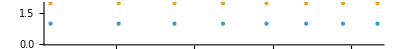

```mathematica
NumberLinePlot[{approxrange,range}]
```

## Source & Additional Information

### Contributed By

Daniele Gregori

### Keywords

range

algebraics

numbers

roots

combinations

closed form

search

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

Range

PowerRange

AlgebraicNumber

AlgebraicIntegerQ

Algebraics

### Related Resource Objects

FindClosedForm

FareyRange

ComplexRange

PrimesBetween

DanieleGregori/GeneralizedRange

### Source/Reference Citation

Source, reference or citation information

### Links

Algebraic Number -- from Wolfram MathWorld

GitHub - Daniele-Gregori/GeneralizedRange

### Tests

MyFunction[x,y]

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Extended functionality is provided in the homonymous function of the paclet "DanieleGregori/GeneralizedRange".

The definition of the "FormulaComplexity" option values in ResourceFunction["FindClosedForm"] will be made uniform with here.

## Submission Notes

Additional information for the reviewer.